# Reject Sampling Monte Carlo

Reject Sampling Monte Carlo

```mathematica
f[x_]:= Exp[0.4(x-0.4)^2-0.08 x^4]
Q1[x_,s_]:=√(1/(2π s^2))Exp[-x^2/(2 s^2)]
```

```mathematica
Q2[x_,s_]:=PDF[CauchyDistribution[0,s],x]
```

```mathematica
CauchyDistribution
```

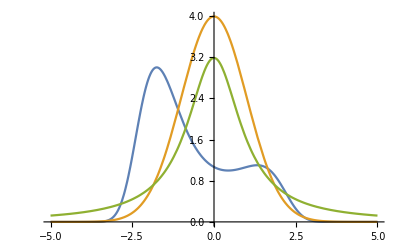

```mathematica
P0=Plot[{f[x],10Q1[x,1],10Q2[x,1]},{x,-5,5}]
```

```mathematica
∫_-5^5 f[x]ⅆx//N
```

7.85218

```mathematica
∫_-5^5 f[x]ⅆx//N
```

```mathematica
x:=10*RandomReal[]-5
```

```mathematica
y:=5*Random[]
```

```mathematica
sx=x;sy=y;
```

```mathematica
f[x]
```

0.998394

```mathematica
f[x]
```

0.00108828

```mathematica
Clear[sx,sy,L,LO];
```

```mathematica
L={};LO={};
```

```mathematica
Timing[For[i=0,i<10001,i++,sx=x;sy=y;If[f[sx]>sy,L=Append[L,{sx,sy}];Clear[sx,sy],LO=Append[LO,{sx,sy}]]]]
```

{0.453546,Null}

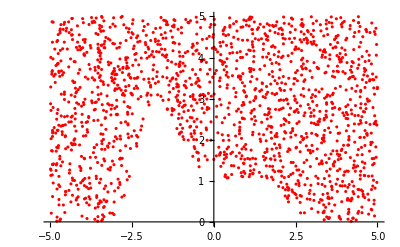

```mathematica
ListPlot[LO,PlotStyle->Red]
```

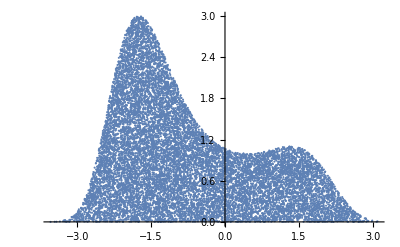

```mathematica
ListPlot[L]
```

```mathematica
Time
```

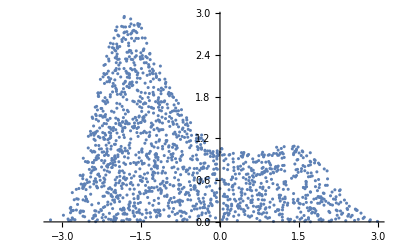

```mathematica
P=ListPlot[L]
```

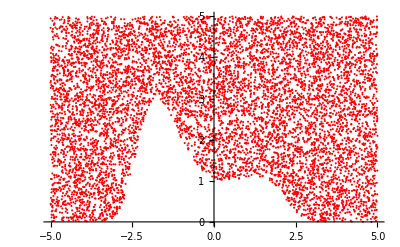

```mathematica
PO=ListPlot[LO,PlotStyle->Red]
```

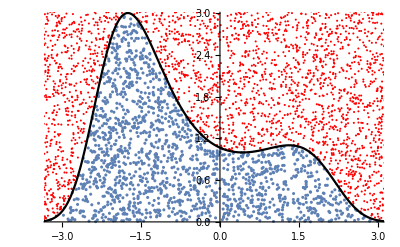

```mathematica
Show[P,PO,P0]
```